# Rough Work

#### Schw metric and computing limits

```mathematica
ClearAll["Global`*"]

r = rbar*(1 + M/(2*rbar))^2

FullSimplify[1-2*M/r]
```

(1+M/(2 rbar))^2 rbar

(M-2 rbar)^2/(M+2 rbar)^2

```mathematica
Clear[r]

M = 1

eq = r == rbar*(1 + M/(2*rbar))^2;

Solve[eq, rbar]
```

1

{{rbar→1/2 (-1+r-√(-2 r+r^2))},{rbar→1/2 (-1+r+√(-2 r+r^2))}}

```mathematica
rbarsolution = rbar /. Solve[eq, rbar][[2]]
```

1/2 (-1+r+√(-2 r+r^2))

```mathematica
Limit[rbarsolution/r, r -> Infinity]
```

1

```mathematica
roverrbar = (1 + M/(2*rbar))^2;

Limit[roverrbar, rbar-> Infinity]
```

1

Checking limit at horizon

```mathematica
rbarsolution /. r -> 2
```

1/2

In line with sarp.

#### TOV stuff

Now to convert the TOV metric to isotropic coords to compute the radial drop.

Solved the differential eqn below and by hand, by hand was better as it was copied from the paper.

```mathematica
eq = D[rbar[r], r] == rbar[r]/(r Sqrt[1 - k^2 r^2]);
FullSimplify[DSolve[eq, rbar, r]] (*Different answer given in paper which i also got*)
```

{{rbar→Function[{r},ⅇ^(-ArcTanh[√(1-k^2 r^2)]) C[1]]}}

General Integration and Differentiation checks

```mathematica
D[-Tanh[x]^2,x] (*Computing a derivative*)
```

-2 Sech[x]^2 Tanh[x]

```mathematica
eq = -1/(Cosh[x]^2 (1 - Tanh[x]^2))
Integrate[eq, x]
```

-Sech[x]^2/(1-Tanh[x]^2)

-x

Final eqn obtained for rbar, more on r on paper in my copy

```mathematica
eq = rbar == C * Sqrt[(1 - Sqrt[1-k^2 r^2])/(1 + Sqrt[1 + k^2 r^2])]
```

rbar==C √((1-√(1-k^2 r^2))/(1+√(1+k^2 r^2)))

#### START from here, all above is metrics and limits.... Doing the Radial drop in isotropic coords

first looking at time in schw coords outside to drop to the Radius of the star.

```mathematica
Clear["Global`*"]
R0 = 20; (*Initial Drop point*)
RStar = 4 ; (*Radius of the Star*)
```

Convert r = 4M and r = 20M to isotropic coords

```mathematica
rSchw[rbar_] = Block[{M = 1}, rbar (1 + M/(2 rbar))^2] (*Block says use this value of M then forget it*)

rBarSchw[r_] = Block[{M = 1}, 1/2 (-M + r + Sqrt[r^2 - 2 M r])]
```

(1+1/(2 rbar))^2 rbar

1/2 (-1+r+√(-2 r+r^2))

Finally converting to isotropic coords

```mathematica
rbar0 = rBarSchw[R0];
rbarStar = rBarSchw[RStar];
```

Defining the Isotropic metric components for external Schwarzschild spacetime

```mathematica
A[rbar_] = Block[{M=1}, (1 + M/(2 rbar))^2];
α[rbar_] = Block[{M=1}, (1 - M/(2 rbar))/(1 + M/(2 rbar))];
```

```mathematica
E0=α[rbar0];
0<E0<=1
Ut0=E0/α[rbar0]^2;
Utdrop[rbar_]=E0/α[rbar]^2;
Urdrop[rbar_]=-1/A[rbar] √(E0^2/α[rbar]^2-1);
```

True

Times:

```mathematica
tSchw[R_,rf_]:=Block[{M=1},-1/(√(2M))NIntegrate[(√(1-2M/R))/(√(1/r-1/R))1/(1-2 M/r),{r,R,rf}]];
(*from MTW book*)
```

```mathematica
tauSchw[RStart_, rFinish_] = Block[{M=1}, 1/Sqrt[2 M] (rFinish RStart Sqrt[1/rFinish - 1/RStart] + RStart^(3/2) ArcTan[Sqrt[RStart/rFinish - 1]]) -(1/Sqrt[2 M] (RStart RStart Sqrt[1/RStart - 1/RStart] + RStart^(3/2) ArcTan[Sqrt[RStart/RStart - 1]]))];
```

```mathematica
tauSchw[20, 4];
```

```mathematica
tauIsotropic[rStart_, rFinish_] :=NIntegrate[1/Urdrop[rBar],{rBar,rStart,rFinish},WorkingPrecision->40]
```

```mathematica
NumericQ@tauIsotropic[rbar0, rbarStar]
Print["Check proper time equality: ",Abs[1-tauSchw[20,4]/tauIsotropic[rbar0,rbarStar]]<10^-16] (*Correct up to here*)
```

True

Check proper time equality: True

#### Doing radial drop pretending to be an observer at infinity

```mathematica
Ut[rbar_,ur_]=1/α[rbar] √(1+ur^2/A[rbar]^2);
drBardt[rbar_, ur_] = 1/(A[rbar]^2 Ut[rbar, ur])ur;
durdt[rbar_, ur_] = -α[rbar] Ut[rbar, ur] Derivative[1][α][rbar] + ur^2/Ut[rbar, ur]((Derivative[1][A][rbar])/A[rbar]^3);
```

not following 2M part of the notebook as we are dealing with a star, so rEnd = 4

```mathematica
t0 = 0;
rEnd=4;
rBarEnd = rBarSchw[rEnd];
tEnd = tSchw[R0, RStar];
sol  = NDSolve[{rbar'[t] == drBardt[rbar[t], ur[t]], ur'[t] == durdt[rbar[t], ur[t]],
rbar[0] == rbar0, ur[0] == 0}, {rbar, ur}, {t, t0, tEnd}][[1]]
```

{rbar→InterpolatingFunction[…],ur→InterpolatingFunction[…]}

```mathematica
(*Extract Solutions and plot*)
rbarNum = rbar /. sol;
urNum = ur /. sol;
```

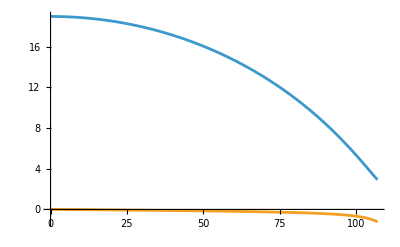

```mathematica
Plot[{rbarNum[t], urNum[t]}, {t, t0, tEnd}] (*rbarNum = blue, urNum = orange*)
```

#### Checking that the simple solution using the analytic integral and ND solving the ODES agree on the same proper time as a function of rbarFinal

```mathematica
tauNDSolve[tf_] := NIntegrate[α[rbarNum[t]]^2/E0, {t, t0, tf}];
```

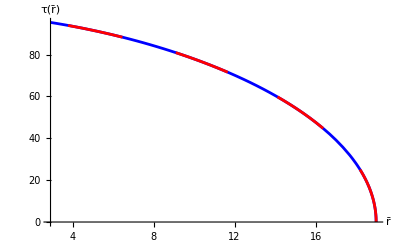

```mathematica
Show[Plot[tauIsotropic[rbar0, r], {r, rbar0, rbarStar}(*Plot from starting r0 down to R, as r decreases*), PlotStyle->Blue]
, ParametricPlot[{rbarNum[tf], tauNDSolve[tf]}, {tf, t0, tEnd},
PlotStyle->{Dashing[0.1], Red}], AxesLabel -> {"r̄", "τ(r̄)"}]
```

```mathematica
tEnd
```

106.934

## Constant density inner solution

## Setting up Everything:

```mathematica
Clear[r]
M = 1;
RStar = 5;
```

#### Interior Solution functions

```mathematica
Mfunc[r_] = Piecewise[{{M r^3/RStar^3, r <= RStar}, {M, r>RStar}}];
grrTOV[r_] = (1 - (2Mfunc[r])/r)^-1; 
κ = √(2 M/RStar^3);
(*Int const*)

Const = rBarSchw[RStar] √((1+√(1-(2M)/RStar))/(1-√(1-2 M/RStar))); (*Can use schw to convert RStar as the value should be the same inside and outside*)

rBarofrInside[r_]=Const √((1-√(1-2 Mfunc[r]/r))/(1+√(1-2 Mfunc[r]/r)));
rofRbarInside[R_]=1/κ √(1-Tanh[Log[R/Const]]^2);
```

Checking Inside and outside transformations agree on RSTAR

```mathematica
rbarStar = rBarSchw[RStar];
RStarVal == N[rofRbarInside[%] /. M -> M /. RStar -> RStar] (*and it matchesm, % takes previous lines answer*)
```

RStarVal==5.

#### Limits as r and rbar go to zero are actually zero in the star

```mathematica
0 == Limit[rBarofrInside[r], r->0]
0 == Limit[rofRbarInside[rbar], rbar -> 0]
```

True

True

Or see limit by analysing the series expansion

```mathematica
0 == Limit[
	FullSimplify[
	Series[rBarofrInside[r], {r, 0, 1} (*Variable we are expanding "r", expand about "0", keep terms up to order "1"*)],
	0 < r < RStar
	],
	r->0
	]

0 == Limit[
	FullSimplify[
	Series[rofRbarInside[rbar], {rbar, 0, 1} (*Variable we are expanding "r", expand about "0", keep terms up to order "1"*)],
	rbar > 0 (*??*)
	],
	rbar->0
	]
```

True

True

#### Lapse and shift functions from metric

```mathematica
αInside[rbar_]=(3/2 √(1-2 M/RStar)-1/2 √(1-2(M r^2)/RStar^3))/.r->rofRbarInside[rbar];
AInside[rbar_]=rofRbarInside[rbar]/rbar;
```

Checking if spacetime is regular at rbar = 0 and it is

```mathematica
ALim0 = Limit[Simplify[Series[AInside[rbar], {rbar, 0, 1}], rbar >0], rbar->0] // N (*Means give it to me as a number*)
alphaLim0 = 
Limit[
Simplify[
Series[αInside[rbar], {rbar, 0, 1}], rbar >0],
rbar -> 0] // N
```

1.4315

0.661895

Plotting functions near the limits?

```mathematica
Show[Plot[AInside[rbar], {rbar, 0, 2}],
Plot[αInside[rbar], {rbar, 0, 2}, PlotStyle->Red],
Graphics[{Blue, Disk[{0,ALim0}, ImageScaled[{0.01, 0.02}]]}],
Graphics[{Red, Disk[{0, alphaLim0}, ImageScaled[{0.01, 0.02}]]}],
PlotRange -> All]
```

-Graphics-

### Constructing ODEs to be solved

```mathematica
UtInside[rbar_,ur_]=1/αInside[rbar] √(1+ur^2/AInside[rbar]^2);
drBardtInside[rbar_, ur_] = 1/(AInside[rbar]^2 UtInside[rbar, ur])ur;
durdtInside[rbar_, ur_] = -αInside[rbar] UtInside[rbar, ur] Derivative[1][αInside][rbar] + ur^2/UtInside[rbar, ur]((Derivative[1][AInside][rbar])/AInside[rbar]^3);
```

### Solving the ODES for the infalling part.

Solver goes cuckoo at r = 0

```mathematica
t0 = 0;
tEnd = 2300;

rStop = 10^-5;

solIn = 
NDSolve[{rbar'[t] ==Piecewise[{{drBardt[rbar[t], ur[t]], rbar[t] >= rbarStar}, {drBardtInside[rbar[t], ur[t]], rbar[t] < rbarStar}}],
ur'[t] == Piecewise[{{durdt[rbar[t], ur[t]],rbar[t] >= rbarStar}, {durdtInside[rbar[t], ur[t]], rbar[t] < rbarStar}}], rbar[0] == rbar0, ur[0] == 0, WhenEvent[rbar[t] == rStop, ur[t] -> -ur[t]]}, {rbar, ur}, {t, t0, tEnd}][[1]]

rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
```

{rbar→InterpolatingFunction[…],ur→InterpolatingFunction[…]}

```mathematica
tCenterCrossing = rbarNumIn["Domain"][[1,2]] (*Domain asks, "Over what time interval are yu defined"*)

(*[[1, 2]] says take the first interval which is {tmin,tmax} and 2 extracts the max time from this.*)
```

2300.

```mathematica
tSurface=t/.FindRoot[rbarNumIn[t]==rbarStar,{t,100,10,2300}(*{variable, initial guess, tmin, tmax}*)] (*t is just a variable here, this returns t ./ {t -> X seconds} ./ replaces all, so then t just becomes the number which becomes tSurface*)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

104.013

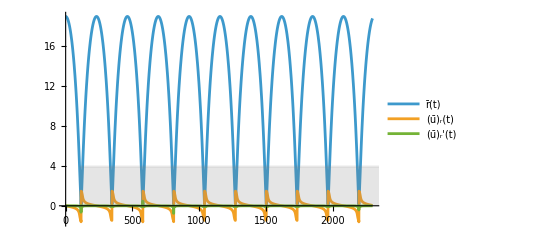

```mathematica
outFig=Show[Plot[{rbarNumIn[t],urNumIn[t],urNumIn'[t]},{t,t0,.999 tCenterCrossing},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]]
,Plot[rbarStar,{t,tSurface,tSurface+tCenterCrossing}, (*[const line, {Domain the line is drawn on}]*)PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]](*Directive means... apply all of these stylings at the same time*)
```

In line with Sarp.

why does it not pick up all the SHMS when i pick a large tEnd?

#### Checking limits for ur as the drag ur is not working when trying to solve for it.

```mathematica
FullSimplify[Limit[durdt[rbar, ur], {rbar->rbarStar, ur -> -.9}]] // N
FullSimplify[Limit[durdtInside[rbar, ur], {rbar->rbarStar, ur -> -.9}]] // N
```

-0.0804377

-0.0804377

### Drag, Accretion and moving to 2D and all that good stuff

```mathematica
(*Hydrodynamic Drag*)
(*Setting up variables*)
m = 10^-6;
Ivariable = 10; (*???*)
η = 1000; (*Speed up parameter*)
ρ = 10;
u[rbar_, ur_] = Abs[ur]/AInside[rbar];
P[rbar_] = ρ((√(1 - 2(M r^2)/RStar^3)-√(1 - 2 M/RStar))/(3 √(1 - 2 M/RStar) - √(1 - 2(M r^2)/RStar^3))) /.r->rofRbarInside[rbar];
(*Derived from TOV as I done last year*)

dpdtdragr[rbar_, ur_] = (-4π αInside[rbar](ρ + P[rbar])m^2(1 + 2 u[rbar, ur]^2)^2 Ivariable ur)/u[rbar, ur]^3;
```

Checking limits to debug the Solver not working

```mathematica
FullSimplify[Limit[P[rbar], rbar -> rbarStar]];
FullSimplify[Limit[P[rbar], rbar -> 0]];
FullSimplify[Limit[AInside[rbar], rbar -> rbarStar]];
FullSimplify[Limit[αInside[rbar], rbar -> rbarStar]];
FullSimplify[Limit[dpdtdragr[rbar, ur], rbar -> rbarStar], ur ∈ Reals];
```

```mathematica
RStar;
rbarStar;
M;
```

#### Creating the ODEs to now solve with drag and plot the result for same tEnd.

```mathematica
durdtInsideDrag[rbar_, ur_] = -αInside[rbar] UtInside[rbar, ur] Derivative[1][αInside][rbar] + ur^2/UtInside[rbar, ur]((Derivative[1][AInside][rbar])/AInside[rbar]^3) + 1/m(dpdtdragr[rbar, ur]);
```

#### Solving the modified ODE with the old ones

```mathematica
t0 = 0;
tEnd = 2300;

rStop = 10^-5;

solIn = 
NDSolve[{rbar'[t] ==Piecewise[{{drBardt[rbar[t], ur[t]], rbar[t] >= rbarStar}, {drBardtInside[rbar[t], ur[t]], rbar[t] < rbarStar}}],
ur'[t] == Piecewise[{{durdt[rbar[t], ur[t]],rbar[t] >= rbarStar}, {durdtInsideDrag[rbar[t], ur[t]], rbar[t] < rbarStar}}], rbar[0] == rbar0, ur[0] == 0, WhenEvent[rbar[t] == rStop, ur[t] -> -ur[t]]}, {rbar, ur}, {t, t0, tEnd}, WorkingPrecision->40][[1]]

rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
```

NDSolve::ndsz: At t == 201.4208336768857283549134388011549502177, step size is effectively zero; singularity or stiff system suspected.

{rbar→InterpolatingFunction[{{0, 201.4208336768857283549134388011549502177}}, <>],ur→InterpolatingFunction[{{0, 201.4208336768857283549134388011549502177}}, <>]}

```mathematica
tCenterCrossing = rbarNumIn["Domain"][[1,2]]
tSurface=t/.FindRoot[rbarNumIn[t]==rbarStar,{t,80,10,tCenterCrossing}]
```

201.4208336768857283549134388011549502177

104.013

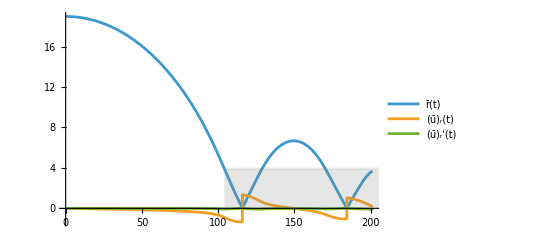

```mathematica
outFig=Show[Plot[{rbarNumIn[t],urNumIn[t],urNumIn'[t]},{t,t0,.999 tCenterCrossing},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]]
,Plot[rbarStar,{t,tSurface,tSurface+tCenterCrossing}, (*[const line, {Domain the line is drawn on}]*)PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]](*Directive means... apply all of these stylings at the same time*)
```

Blowing up at surface of the star

```mathematica
FullSimplify[Limit[durdtInsideDrag[rbar, ur], {rbar->rbarStar, ur -> -.9}]]  // N
FullSimplify[Limit[durdt[rbar, ur], {rbar->rbarStar, ur -> -.9}]] // N
-FullSimplify[Limit[durdtInsideDrag[rbar, ur], {rbar->rbarStar, ur -> -.9}]]+FullSimplify[Limit[durdt[rbar, ur], {rbar->rbarStar, ur -> -.9}]] // N
FullSimplify[Limit[drBardt[rbar, ur], {rbar->rbarStar, ur -> -.9}]] // N;
FullSimplify[Limit[drBardtInside[rbar, ur], {rbar->rbarStar, ur -> -.9}]] // N;
FullSimplify[Limit[dpdtdragr[rbar, ur], {rbar->rbarStar, ur -> -.9}]] // N
(*rbar(t) is fine, ur(t) is the problem, it is not continuous over the surface of the star*)
```

-0.0705468

-0.0804377

-0.00989095

9.89095×10^-9

```mathematica
FullSimplify[Limit[durdt[rbar,ur],{rbar->rbarStar, ur -> -0.9}]-Limit[durdtInsideDrag[rbar,ur],{rbar->rbarStar, ur -> -0.9}]]
```

-0.00989095

After implementing machine precision, this fixed the issue, but with speed up parameter, we are no longer continuous at rbarStar and everything breaks down inside.

### Adding in phi component to the equations to make the orbits elliptical (quickly)

#### Outside Star

```mathematica
Clear[ur, rbar, uphi]
```

```mathematica
umagphi[rbar_, uphi_] = Abs[uphi]/AInside[rbar];
```

```mathematica
(*OUTSIDE STAR*)
dphidtOutside[rbar_,ur_, uphi_] = 1/(rbar^2*A[rbar]^2*Ut[rbar, ur])uphi;

durdt2DOutside[rbar_, ur_, uphi_] = -α[rbar] Ut[rbar, ur] Derivative[1][α][rbar] + ur^2/Ut[rbar, ur]((Derivative[1][A][rbar])/A[rbar]^3) + uphi^2/Ut[rbar, ur](1/(rbar^3 *A[rbar]^2) + (Derivative[1][A][rbar])/(rbar^2*A[rbar]^3));
```

#### Inside Star

```mathematica
dphidtInside[rbar_, ur_, uphi_] = 1/(rbar^2 AInside[rbar]^2 UtInside[rbar, ur])uphi;

dpdtdragphi[rbar_, uphi_] = 1/umagphi[rbar, uphi]^3(-4π αInside[rbar]*(ρ + P[rbar])*m^2*(1 + 2 umagphi[rbar, uphi]^2)^2 *Ivariable *uphi);

duphidtInside[rbar_, uphi_] = 1/m(dpdtdragphi[rbar, uphi]);
durdt2DInside[rbar_, ur_, uphi_] = -αInside[rbar] UtInside[rbar, ur] Derivative[1][αInside][rbar] + ur^2/UtInside[rbar, ur]((Derivative[1][AInside][rbar])/AInside[rbar]^3) + uphi^2/UtInside[rbar, ur](1/(rbar^3 AInside[rbar]^2) + (Derivative[1][AInside][rbar])/(rbar^2 AInside[rbar]^3)) +  1/m(dpdtdragr[rbar, ur]);
```

#### Solving the ODEs

```mathematica
t0 = 0;
tEnd = 2300;

rStop = 10^-5;

solIn = 
NDSolve[{rbar'[t] ==Piecewise[{{drBardt[rbar[t], ur[t]], rbar[t] >= rbarStar}, {drBardtInside[rbar[t], ur[t]], rbar[t] < rbarStar}}],
ur'[t] == Piecewise[{{durdt2DOutside[rbar[t], ur[t], uphi[t]],rbar[t] >= rbarStar}, {durdt2DInside[rbar[t], ur[t], uphi[t]], rbar[t] < rbarStar}}],
uphi'[t] == Piecewise[{{0, rbar[t] >= rbarStar},
{duphidtInside[rbar[t], uphi[t]], rbar[t] < rbarStar}}],
phi'[t] == Piecewise[{{dphidtOutside[rbar[t], ur[t], uphi[t]], rbar[t] >= rbarStar},
{dphidtInside[rbar[t], ur[t],  uphi[t]], rbar[t] < rbarStar}}],
rbar[0] == rbar0, ur[0] == 0, phi[0] == 0, uphi[0] == 0, WhenEvent[rbar[t] == rStop, {ur[t] -> -ur[t], phi[t] -> phi[t] + π}]}, {rbar, ur, phi, uphi}, {t, t0, tEnd}, WorkingPrecision->40][[1]]
```

Power::infy: Infinite expression 1/0^3 encountered.

Infinity::indet: Indeterminate expression (0 π ComplexInfinity)/(√10) encountered.

NDSolve::nlnum: The function value {-0.3520905189568709057012657411270176721211,-0.07044147778137212474618129525816077187248,0,Indeterminate} is not a list of numbers with dimensions {4} at {t,rbar[t],ur[t],phi[t],uphi[t],NDSolve`s$55911[t],NDSolve`s$55912[t]} = {104.012901593537830160666038209778530713,3.936491673103708442589632699891199805416,-0.8981433722035953056180180130514575973967,0,0,1,-1}.

NDSolve::smpf: Failure to project onto the discontinuity surface when computing Filippov continuation at time 104.012901593537830160666038209778530713.

{rbar→InterpolatingFunction[…],ur→InterpolatingFunction[…],phi→InterpolatingFunction[…],uphi→InterpolatingFunction[…]}

```mathematica
rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
phiNumIn = phi /. solIn;
uphiNumIn = uphi /. solIn;
```